```mathematica
SetDirectory[NotebookDirectory[]];
```

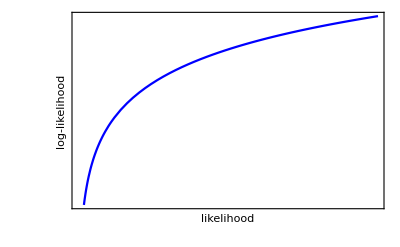

```mathematica
g1=Plot[Log[L],{L,0,20},Frame->{True,True,False,False},FrameTicks->{False,False},Axes->{False,True},FrameLabel->{"likelihood","log-likelihood"},PlotStyle->Blue,BaseStyle->Medium]
```

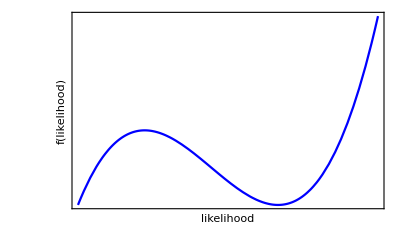

```mathematica
g2=Plot[L^2+L^3,{L,-1,0.5},Frame->{True,True,False,False},FrameTicks->{False,False},Axes->{False,False},FrameLabel->{"likelihood","f(likelihood)"},PlotStyle->Blue,BaseStyle->Medium]
```

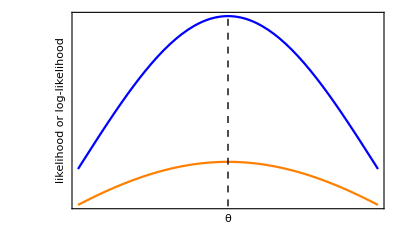

```mathematica
g3=Plot[{PDF[NormalDistribution[0,5],x],PDF[NormalDistribution[0,8],x]},{x,-5,5},Axes->{True,False},Frame->{True,True,False,False},FrameTicks->{False,False},FrameLabel->{"θ","likelihood or log-likelihood"},PlotStyle->{Blue,Orange},Epilog->{Dashed,Line[{{0,0},{0,PDF[NormalDistribution[0,5],0]}}]},BaseStyle->Medium]
```

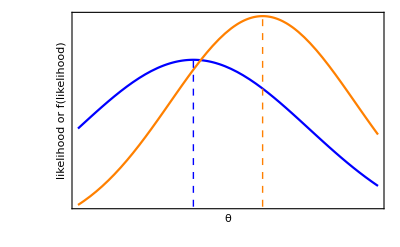

```mathematica
g4=Plot[{PDF[NormalDistribution[0,5],x],PDF[NormalDistribution[3,4],x]},{x,-5,8},Axes->{True,False},Frame->{True,True,False,False},FrameTicks->{False,False},FrameLabel->{"θ","likelihood or f(likelihood)"},PlotStyle->{Blue,Orange},Epilog->{{Blue,Dashed,Line[{{0,0},{0,PDF[NormalDistribution[0,5],0]}}]},{Orange,Dashed,Line[{{3,0},{3,PDF[NormalDistribution[3,4],3]}}]}},BaseStyle->Medium]
```

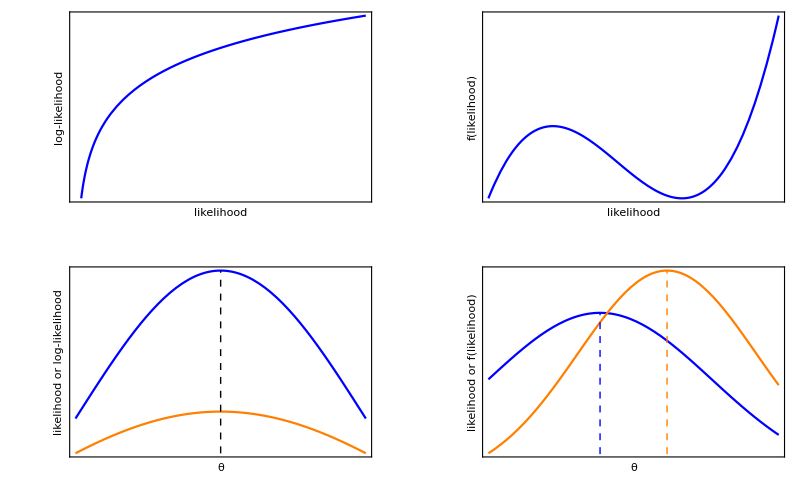

```mathematica
gFinal=Show[GraphicsGrid[{{g1,g2},{g3,g4}}],ImageSize->800]
```

```mathematica
Export["Likelihood_logMonotonicity.pdf",gFinal]
```

Likelihood_logMonotonicity.pdf